```mathematica
(* Sets the Base directory, changing which files are easiest to acces. *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns","18-04-18","data"}];
If[SystemInformation["Kernel","OperatingSystem"]=="Unix",
folder=FileNameJoin[{"/","home","karl",dropBoxOn}]; ,(* Home coputer is Linux, so needs "/" at beginning *)
folder=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"*)
];

(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{folder}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=Length[directories],i>0,i--,
Print[i -> directories[[i]]];]
(* set rootFolder to the folder name containing the desired Files *)
rootFolder=FileNameJoin[{dataFolder}];
SetDirectory[rootFolder];
(* Obtain the filenames of the excitation functions and print them out.*)
SetDirectory[FileNameJoin[{folder}]];
files=FileNames["EX*.dat"]
```

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-04-18\data

{EX2018-04-18_142916.dat,EX2018-04-18_150048.dat,EX2018-04-18_170656.dat,EX2018-04-18_170951.dat,EX2018-04-18_171257.dat,EX2018-04-18_171705.dat,EX2018-04-18_172010.dat,EX2018-04-18_172240.dat,EX2018-04-19_110734.dat,EX2018-04-19_111633.dat,EX2018-04-19_111844.dat,EX2018-04-19_112059.dat,EX2018-04-19_112305.dat,EX2018-04-19_112603.dat,EX2018-04-19_115930.dat,EX2018-04-19_120210.dat,EX2018-04-19_120703.dat,EX2018-04-19_121501.dat,EX2018-04-19_121714.dat,EX2018-04-19_121937.dat,EX2018-04-19_122157.dat,EX2018-04-19_150028.dat,EX2018-04-19_150445.dat,EX2018-04-19_150804.dat,EX2018-04-19_154231.dat,EX2018-04-19_155319.dat,EX2018-04-19_155824.dat,EX2018-04-19_161257.dat,EX2018-04-19_161509.dat,EX2018-04-19_161723.dat,EX2018-04-19_162001.dat,EX2018-04-19_162226.dat,EX2018-04-19_162520.dat,EX2018-04-19_171948.dat,EX2018-04-19_172150.dat,EX2018-04-19_172351.dat,EX2018-04-19_172610.dat,EX2018-04-19_172819.dat,EX2018-04-19_173108.dat,EX2018-04-19_215018.dat,EX2018-04-19_215244.dat,EX2018-04-19_215510.dat,EX2018-04-19_215833.dat,EX2018-04-19_220056.dat,EX2018-04-19_223758.dat,EX2018-04-19_224112.dat,EX2018-04-19_224454.dat,EX2018-04-19_224718.dat,EX2018-04-19_225501.dat,EX2018-04-19_232709.dat,EX2018-04-19_232933.dat,EX2018-04-19_233445.dat,EX2018-04-19_233650.dat,EX2018-04-19_233909.dat}

## Performs Gaussian Analysis of Excitation Function (both with counts and current)

```mathematica
allInfo=<||>;
For[i=1,i≤Length[files],i++,
data=ExcitationFunctionProcessor[files,files[[i]]];
info=<|data["Filename"]->data|>;
AppendTo[allInfo,info];
];
Dataset[allInfo]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

LinearAlgebra`BLAS`TRSV::oflow: Machine overflow encountered during computations.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

LinearAlgebra`BLAS`TRSV::oflow: Machine overflow encountered during computations.

General::stop: Further output of LinearAlgebra`BLAS`TRSV::oflow will be suppressed during this calculation.

Dataset[<>]

```mathematica
Normal[d[Values,{"stackedPlot"}][[1]]][[1]]
```

-Graphics-

```mathematica
d=Dataset[allInfo];
Keys[d[[1]]]
```

Dataset[<>]

```mathematica
d[Values,{"Filename","CellTemp(Res)","CVGauge(N2)(Torr)","Comments"}]
```

Dataset[<>]

## Shows Graphs for the normalization process of the excitation function

{2064.76,2112.08,2067.81,2034.99,2032.7,2022.01,2025.07,2025.07,2051.78,2086.13,2060.94,2022.01,2006.75,2075.45,2047.97,2038.04,2025.83,2007.51,1993.01,1916.68,1905.23,1882.33,1902.94,1839.58,1857.9,1854.85,1799.13,1737.3,1705.24,1711.35,1673.94,1646.46,1607.54,1569.37,1544.94,1477.77,1453.35,1412.89,1377.78,1331.98,1303.74}

{9.36671,9.34576,9.59953,9.83887,9.85635,9.99748,9.96657,9.98928,9.88751,9.69546,9.78631,9.97423,10.083,9.70392,9.7267,9.6215,9.30384,8.9215,8.08124,6.06622,2.70256,0.454224,0.225441,0.190804,0.15609,0.12346,0.122281,0.123755,0.116699,0.130891,0.150543,0.166418,0.11135,0.0605338,0.0323637,0.0223309,0.0123852,0.018402,0.0225,0.0195198,0.0184086}

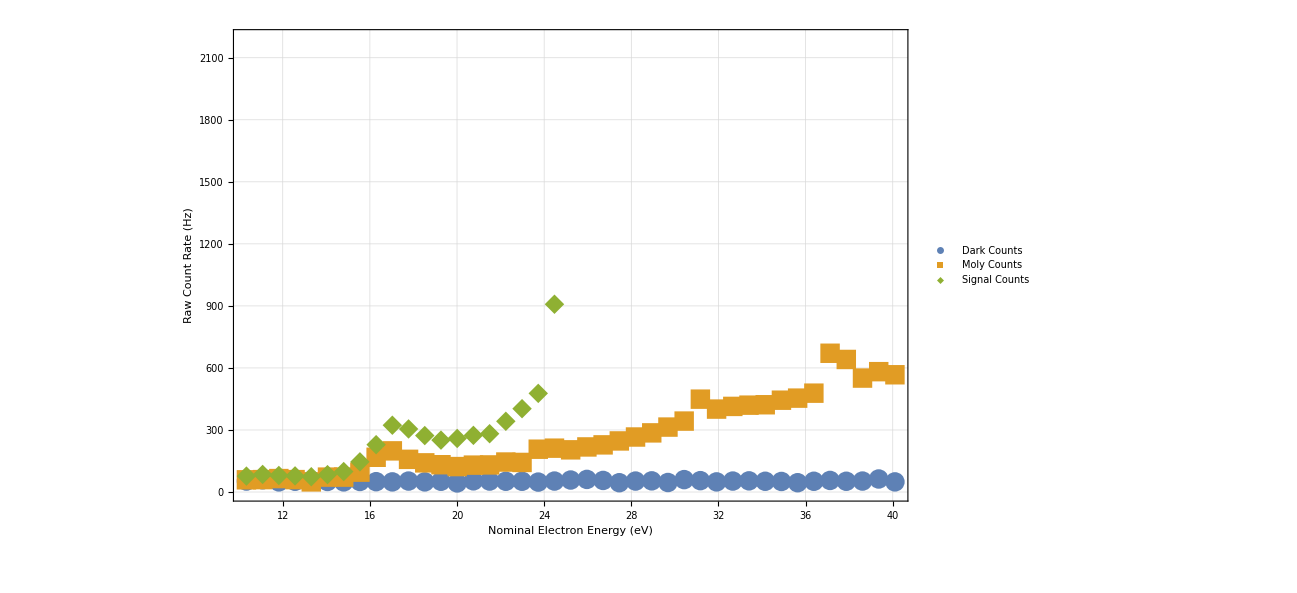

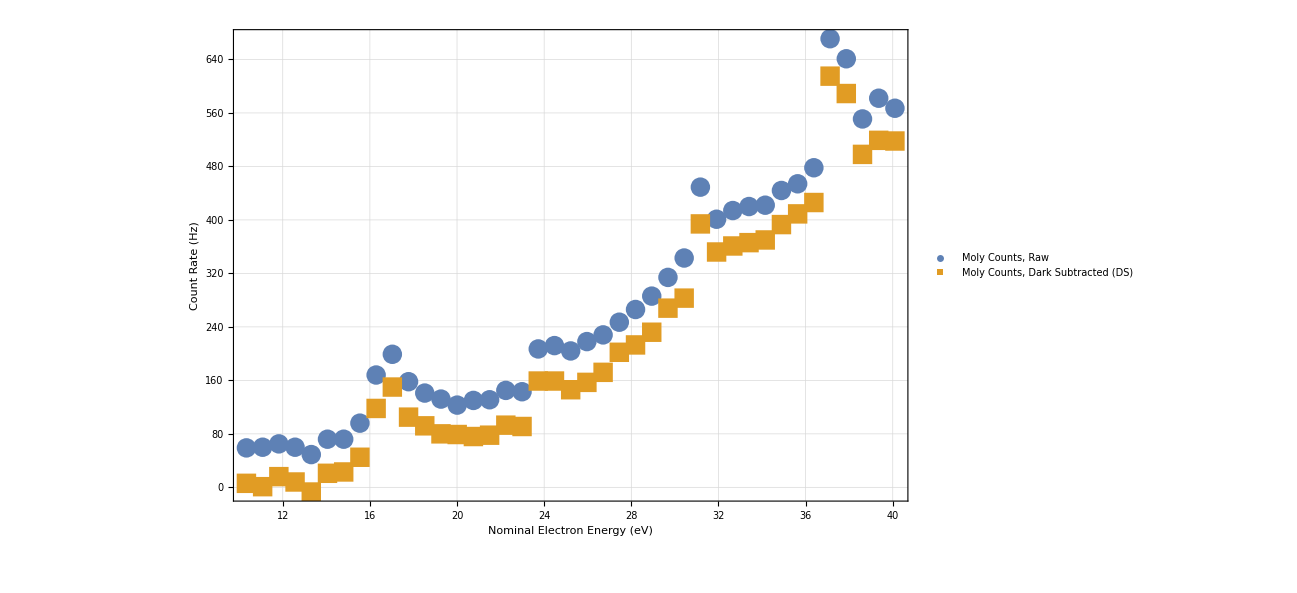

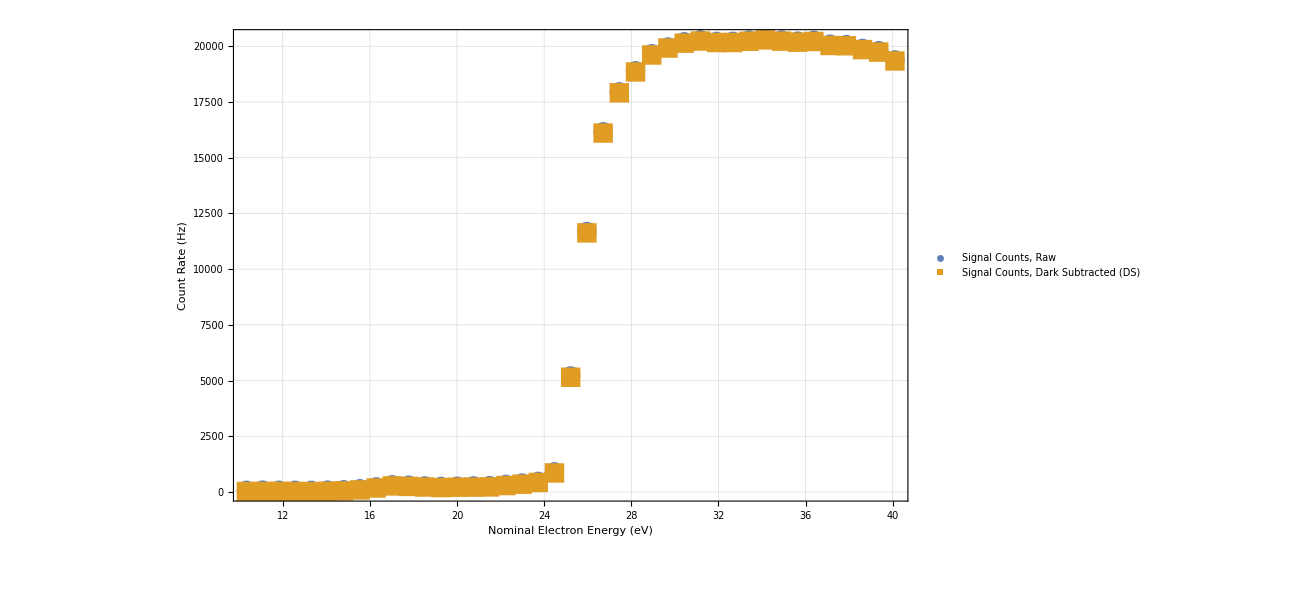

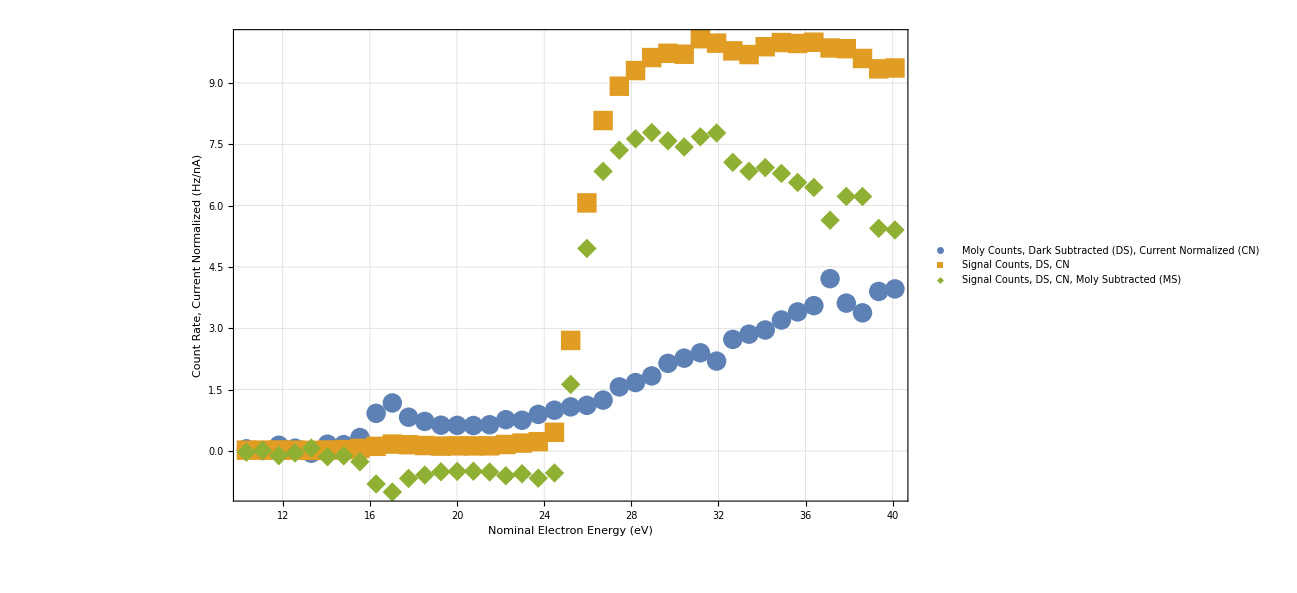

1.60192

1.30091

{{40.1,4.95797},{39.3558,4.99506},{38.6117,5.7085},{37.8675,5.71006},{37.1234,5.17695},{36.3792,5.91222},{35.635,6.02428},{34.8909,6.22698},{34.1467,6.358},{33.4025,6.27554},{32.6584,6.47602},{31.9142,7.13518},{31.17,7.04909},{30.4259,6.82155},{29.6817,6.95877},{28.9376,7.14445},{28.1934,7.00239},{27.4492,6.74843},{26.7051,6.27411},{25.9609,4.54346},{25.2167,1.49158},{24.4726,-0.495991},{23.7284,-0.612973},{22.9843,-0.512618},{22.2401,-0.557158},{21.4959,-0.473618},{20.7518,-0.456624},{20.0076,-0.459699},{19.2634,-0.469461},{18.5193,-0.542165},{17.7751,-0.617487},{17.0309,-0.922953},{16.2868,-0.741188},{15.5426,-0.244292},{14.7985,-0.110754},{14.0543,-0.130245},{13.3101,0.0630734},{12.566,-0.0447064},{11.8218,-0.105908},{11.0776,0.0100458},{10.3335,-0.0299147}}

```mathematica
dataFolderDate="18-02-13";
darkTimeStamp="120100";
darkData=GetFileDataset[files[[GetIndexOfFilenameFromTimestamp[files,darkTimeStamp]]]];
darkHeader=GetFileHeaderInfo[files[[GetIndexOfFilenameFromTimestamp[files,darkTimeStamp]]]];

molyTimeStamp="141849";
molyData=GetFileDataset[files[[GetIndexOfFilenameFromTimestamp[files,molyTimeStamp]]]];
molyHeader=GetFileHeaderInfo[files[[GetIndexOfFilenameFromTimestamp[files,molyTimeStamp]]]];

signalTimeStamp="192323";
signalData=GetFileDataset[files[[GetIndexOfFilenameFromTimestamp[files,signalTimeStamp]]]];
signalHeader=GetFileHeaderInfo[files[[GetIndexOfFilenameFromTimestamp[files,signalTimeStamp]]]];

energyOffset=0;
nA=1*10^-9;
torrTomTorr=1000;
darkCounts=Normal[darkData[All,{"SecondaryElectronEnergy","CountRate","Current"}][All,Values]];
energyArray=Transpose[darkCounts][[1]]+energyOffset;
darkCountArray=Transpose[darkCounts][[2]];

molyCounts=Normal[molyData[All,{"SecondaryElectronEnergy","CountRate","Current"}][All,Values]];
molyCountArray=Transpose[molyCounts][[2]];
molyCurrentMag=molyHeader["#MagnitudeOfCurrent(*10^-X):"];
molyCurrentArrayNa=Transpose[molyCounts][[3]]*10^(-molyCurrentMag)/nA;
ListPlot[{Transpose[{energyArray,darkCountArray}],Transpose[{energyArray,molyCountArray}]}];
molyDarkSubtracted=molyCountArray-darkCountArray;
molyCurrentNorm=molyDarkSubtracted/molyCurrentArrayNa;

signalCounts=Normal[signalData[All,{"SecondaryElectronEnergy","CountRate","Current"}][All,Values]];
signalCountArray=Transpose[signalCounts][[2]];
signalEnergyArray=Transpose[signalCounts][[1]]+energyOffset;
signalCurrentMag=signalHeader["#MagnitudeOfCurrent(*10^-X):"];
signalCurrentArrayNa=Transpose[signalCounts][[3]]*10^(-signalCurrentMag)/nA
signalDarkSubtracted=signalCountArray-Take[darkCountArray,{1,Length[signalCountArray]}];
signalCurrentNorm=signalDarkSubtracted/signalCurrentArrayNa
signalMolySubtracted=signalCurrentNorm-Take[molyCurrentNorm,{1,Length[signalCountArray]}];
signalHeNorm=signalMolySubtracted/(signalHeader["#CVGauge(He)(Torr):"]*torrTomTorr);

xAxisLabel="Nominal Electron\nEnergy (eV)";
yAxisLabel="Raw Count Rate (Hz)";
rawCountsPlot=ListPlot[{Legended[Drop[darkCounts,None,{-1}],"Dark Counts"],Legended[Drop[molyCounts,None,{-1}],"Moly Counts"],Legended[Drop[signalCounts,None,{-1}],"Signal Counts"]},AxesLabel->{xAxisLabel,yAxisLabel},GridLines->Automatic]

yAxisLabel="Count Rate (Hz)";
molyCountsPlot=ListPlot[{Legended[Transpose[{energyArray,molyCountArray}],"Moly Counts, Raw"],Legended[Transpose[{energyArray,molyDarkSubtracted}],"Moly Counts, Dark Subtracted (DS)"]},AxesLabel->{xAxisLabel,yAxisLabel}]

yAxisLabel="Count Rate (Hz)";
signalCountsPlot=ListPlot[{Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalCountArray}],"Signal Counts, Raw"],Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalDarkSubtracted}],"Signal Counts, Dark Subtracted (DS)"]},AxesLabel->{xAxisLabel,yAxisLabel}]

yAxisLabel="Count Rate,\nCurrent Normalized (Hz/nA)";
currentNormalizedPlot=ListPlot[{Legended[Transpose[{energyArray,molyCurrentNorm}],"Moly Counts, Dark Subtracted (DS),\nCurrent Normalized (CN)"],Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalCurrentNorm}],"Signal Counts, DS, CN"],
Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalMolySubtracted}],"Signal Counts, DS, CN, Moly Subtracted (MS)"]
},AxesLabel->{xAxisLabel,yAxisLabel}]

Mean[molyCurrentNorm]
StandardDeviation[molyCurrentNorm]

fullyNormalizedExcitationFunction=Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalHeNorm}]

Export[dataFolderDate<>"_exFnRawCounts.png",rawCountsPlot,ImageResolution->200];
Export[dataFolderDate<>"_exFnMolyCounts.png",molyCountsPlot,ImageResolution->200];
Export[dataFolderDate<>"_exFnSignalCounts.png",signalCountsPlot,ImageResolution->200];
Export[dataFolderDate<>"_exFnCurrentNormalized.png",currentNormalizedPlot,ImageResolution->200];
```

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large,PlotStyle->{Automatic,20},LabelStyle->27,GridLines->Automatic];
SetOptions[ListPlot,BaseStyle->{FontSize->24},ImageSize->Large,PlotMarkers->{Automatic,20},LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];
SetOptions[ListLogPlot,BaseStyle->{FontSize->24},ImageSize->Large,PlotMarkers->{Automatic,20},LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];

nA=1*^-9;
plotLabel="Plot Label";
yAxisLabel="Y";
xAxisLabel="X";
ps={LabelStyle->18,PlotLabel->plotLabel,AxesLabel->{xAxisLabel,yAxisLabel}}

GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];

GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,rawFile[[k]][[1]]->joinedWithSpaces];
,
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];

GaussianAnalyzer[files_,timeString_,dependentVariableString_]:=Module[{fitInfo, bothPlot, derivativePlot,entry,file,ps,header,data,energy,energyDiff,depVar,depVarDiff,energyOneRemoved,depVarDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,dataLabel1,dataLabel2,x1,y1,offset, new23,plot,derPlot,index},
index=GetIndexOfFilenameFromTimestamp[files,timeString];
file=files[[index]];
entry=<||>;

header=GetFileHeaderInfo[file];
data=GetFileDataset[file];
energy=Reverse[Normal[data[All,"SecondaryElectronEnergy"]]];
depVar=Reverse[Normal[data[All,dependentVariableString]]];
depVarDiff=Differences[depVar];
energyDiff=Differences[energy];
energyOneRemoved=Take[energy,{1,-2}];
depVarDer=depVarDiff/energyDiff;
plot=ListPlot[Transpose[{energy,depVar}],PlotLabel->dependentVariableString<>" vs. Energy: "<>timeString,FrameLabel->{"'Slow' Electron Energy (eV)",dependentVariableString},Frame->True];
derPlot=ListPlot[Transpose[{energyOneRemoved,depVarDer}],PlotLabel->dependentVariableString<>" Derivative\nvs. Energy: "<>timeString,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"},Frame->True];


plotTitle="Gaussian Analysis";

plotData=Transpose[{energy,depVar}];
plotData2=Transpose[{energyOneRemoved,depVarDer}];


(*
yAxisTitle="d(Counts)/d(Energy)";
xAxisTitle="Electron Energy (eV)";
*)
dataLabel1="Data";
dataLabel2="Derivative";

ps={ImageSize->Large, PlotLabel->plotTitle,AxesLabel->{"X","Y"}};

plotData=plotData2;
gaussModel[x_]=ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
(*Find the position of the peak of the derivative data*)
maxDerPos=Position[depVarDer,Max[depVarDer]][[1]];
energyOfPeak=energyOneRemoved[[maxDerPos]][[1]];

fit=NonlinearModelFit[plotData,gaussModel[x],{ampl,{m,energyOfPeak},{σ,.9}},x];
model=Normal[fit];
pe=fit["BestFitParameters"]; (*Parameter Estimates*)
errors=fit["ParameterErrors"];

new23=m-(2*Sqrt[2Log[10]]σ)/2/.pe;
offset=23-new23;



x1=energyOfPeak-(3σ/.pe);
y1=.25*(ampl)/.pe;
fitInfo=StringForm["μ=``± ``\nσ=``±``",NumberForm[m/.pe,3],NumberForm[errors[[2]],1],NumberForm[σ/.pe,3],NumberForm[errors[[3]],1]];
(*Print[Show[{Plot[gaussModel[x]/.pe,{x,energyOfPeak-5,energyOfPeak+5},PlotRange->All,PlotLabel->"Gaussian Fit To Derivative\nof "<>dependentVariableString<>" Analysis: "<> timeString,Frame->True,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"}],
Graphics[Text[fitInfo,{x1,y1}],BaseStyle->15],
ListPlot[plotData,PlotLabel->"PLOT2"]}]];*)
bothPlot=ListPlot[{Legended[plotData,dataLabel2],Legended[plotData2,dataLabel1]}];
derivativePlot=ListPlot[Legended[plotData2,dataLabel2],ps];

AppendTo[entry,header];
AppendTo[entry,<|dependentVariableString<>"plot"->plot,"N2Offset"-> data[1,"N2Offset"],"filBias"-> data[1,"bias"],dependentVariableString<>"onsetEnergy"-> m/.pe,dependentVariableString<>"onsetWidth"->  σ/.pe,dependentVariableString<>"lowEnergySignal"-> depVar[[1]],dependentVariableString<>"highEnergySignal"-> depVar[[-1]]|>];
entry
];

ExcitationFunctionProcessor[files_,timeString_]:=Module[{file,ps,header,data,energy,energyDiff,current,currentDiff,energyOneRemoved,currentDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,x1,y1,return ,i},
return=<||>;
AppendTo[return,GaussianAnalyzer[files,timeString,"CountRate"]];
AppendTo[return,GaussianAnalyzer[files,timeString,"Current"]];
i=GetIndexOfFilenameFromTimestamp[files,timeString];
AppendTo[return,"stackedPlot"->StackedExFnPlot[files[[i]] ] ];
return
];

GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];

GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"-> "",":"->""}]->joinedWithSpaces];
,
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"->"",":"->""}]->rawFile[[k]][[2]]];
];
k++;
];
association
];

StackedExFnPlot[fileName_]:=Module[{
fd (*fileDataset*),
fh(*fileHeaderInfo*),
scale(*the magnitude of the faraday cup current *),
temp(*The temperature of the reservoir (mislabeled as the target)*),
pN2(*The pressure on the collision cell convectron gauge*),
data1,data2,
totHe,counts,curr,
paddingx,paddingy,padding, options, spacing,
countsAndCurrent
},
fd=GetFileDataset[fileName];
fh=GetFileHeaderInfo[fileName];
scale=fh["MagnitudeOfCurrent(*10^-X)"];
temp=fh["CellTemp(Targ)"];
pN2=fh["CVGauge(N2)(Torr)"];
data1=fd[All,{"TotalHeOffset","CountRate"}];
{totHe,counts}=Transpose[Normal[data1[Values]]];
data1=Transpose[{totHe*(-1),counts}];
data2=fd[All,{"TotalHeOffset","Current"}];
{totHe,curr}=Transpose[Normal[data2[Values]]];
data2=Transpose[{totHe*(-1),curr*10^-scale/nA}];

paddingx=120;
paddingy=100;
padding={{paddingx,0},{paddingy,30}};
options={ImagePadding->padding,Frame->True};
spacing={0,-150};
GraphicsGrid[{{Show[ListLogPlot[data1,FrameTicks->{None,Automatic},options,FrameLabel->{None,"Count Rate (Hz)"},PlotRange->{Automatic,{50,5500}},GridLines->Automatic],Graphics[Text["temp="<>ToString[temp]<>"  BGP="<>ToString[pN2]<>"\nbias="<>ToString[fd[All,"bias"][[1]]]<>" N2Off="<>ToString[fd[All,"N2Offset"][[1]]],{Center,Top},{0,2}],BaseStyle->15]]},{ListPlot[data2,options,FrameLabel-> {"He Potential","Current (nA)"}]}},Spacings->spacing]
];

TwoAxisListPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},
(*Graphs the data for both sets of plots *)
{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];
(*Pulls the ranges from the plots *)
{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};
(*Grabs where each of the tick marks are in the f plot *)
fticks=N@FindDivisions[frange,5];
(*Finds what tick marks the G plot has at the fPlot Range.*)
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

{LabelStyle→18,PlotLabel→Plot Label,AxesLabel→{X,Y}}

## E_i=2eV

{EX2018-04-18_142916.dat,EX2018-04-18_150048.dat,EX2018-04-18_170656.dat,EX2018-04-18_170951.dat,EX2018-04-18_171257.dat,EX2018-04-18_172010.dat,EX2018-04-18_172240.dat}

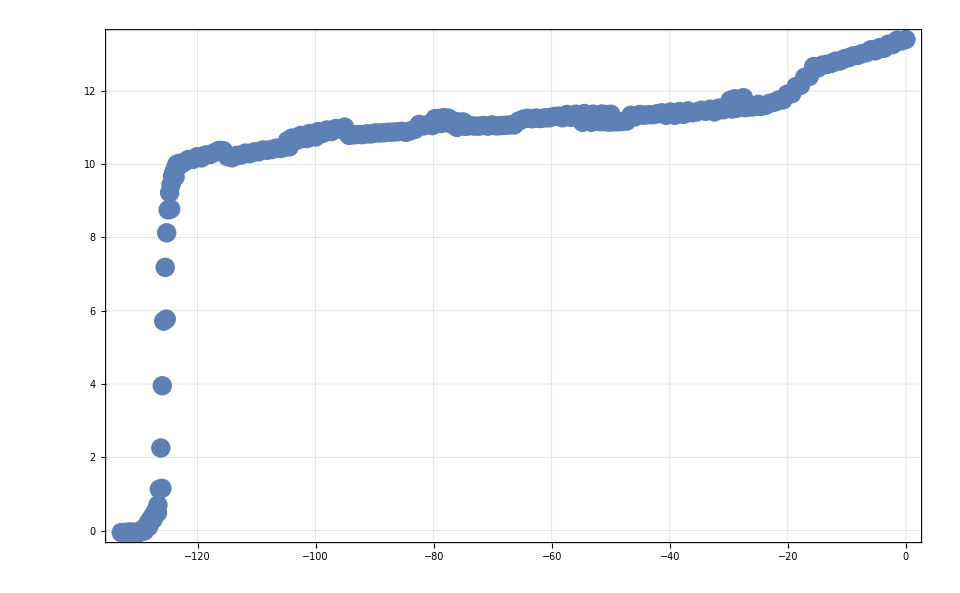

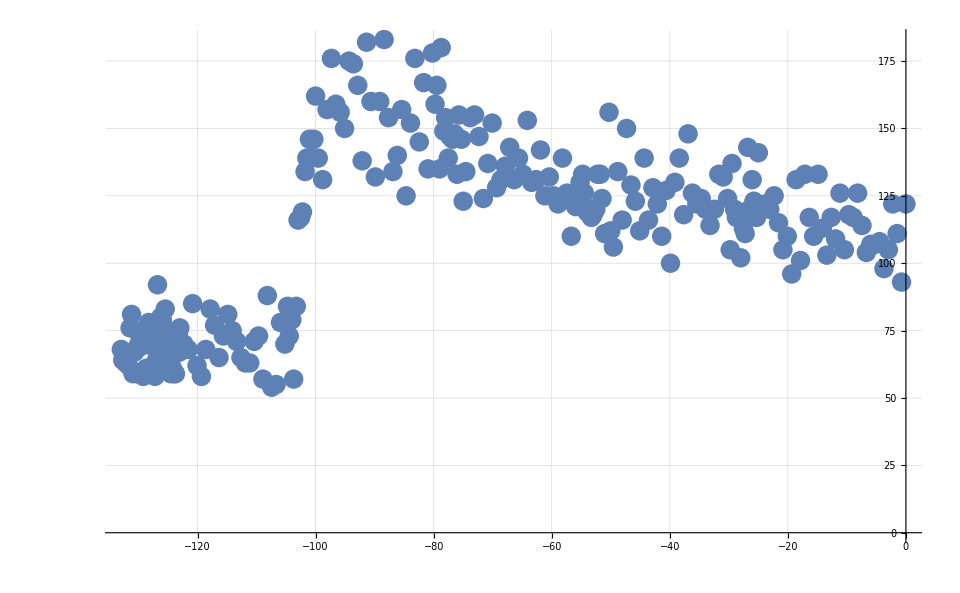

```mathematica
Clear[allDat];
cleanedFiles=Join[Take[files,{1,5}],Take[files,{7,8}]]
cleanedFiles=files;
start=9;
end=14;
For[i=start,i≤ end,i++,
header=GetFileHeaderInfo[cleanedFiles[[i]]];
magnitude=header["MagnitudeOfCurrent(*10^-X)"];
dat=GetFileDataset[files[[i]]];
newDat=dat[All,<|#,"Current(nA)"-> #Current*10^(-magnitude+9)|>&];
If[i==start,allDat=newDat,allDat=Join[allDat,newDat]]
];
ListPlot[allDat[All,{"TotalHeOffset","Current(nA)"}],PlotRange->Full,GridLines->Automatic,Frame->True,Ticks->Automatic]
ListPlot[allDat[All,{"TotalHeOffset","CountRate"}]]
```

## E_i=30eV, Sweep=2 eV

{EX2018-04-18_142916.dat,EX2018-04-18_150048.dat,EX2018-04-18_170656.dat,EX2018-04-18_170951.dat,EX2018-04-18_171257.dat,EX2018-04-18_172010.dat,EX2018-04-18_172240.dat}

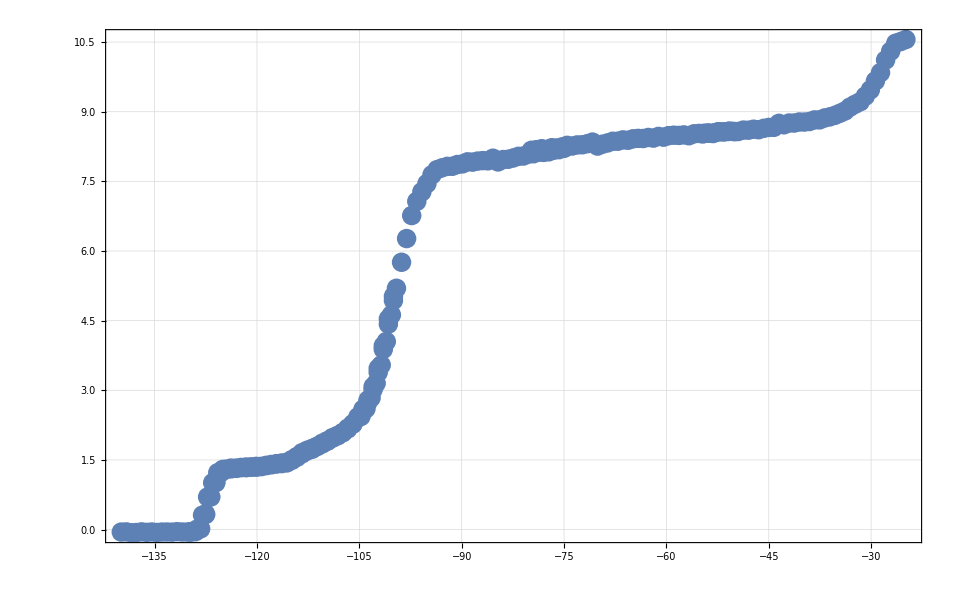

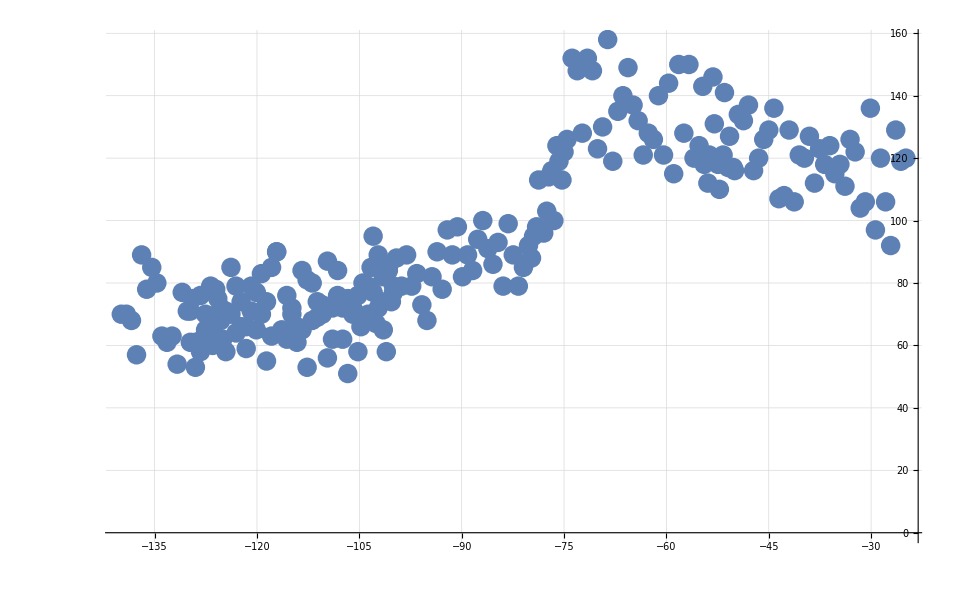

```mathematica
Clear[allDat];
cleanedFiles=Join[Take[files,{1,5}],Take[files,{7,8}]]
cleanedFiles=files;
start=16;
end=21;
For[i=start,i≤ end,i++,
header=GetFileHeaderInfo[cleanedFiles[[i]]];
magnitude=header["MagnitudeOfCurrent(*10^-X)"];
dat=GetFileDataset[files[[i]]];
newDat=dat[All,<|#,"Current(nA)"-> #Current*10^(-magnitude+9)|>&];
If[i==start,allDat=newDat,allDat=Join[allDat,newDat]]
];
ListPlot[allDat[All,{"TotalHeOffset","Current(nA)"}],PlotRange->Full,GridLines->Automatic,Frame->True,Ticks->Automatic]
ListPlot[allDat[All,{"TotalHeOffset","CountRate"}]]
```

## E_i=30eV, Sweep=19 eV

{EX2018-04-18_142916.dat,EX2018-04-18_150048.dat,EX2018-04-18_170656.dat,EX2018-04-18_170951.dat,EX2018-04-18_171257.dat,EX2018-04-18_172010.dat,EX2018-04-18_172240.dat}

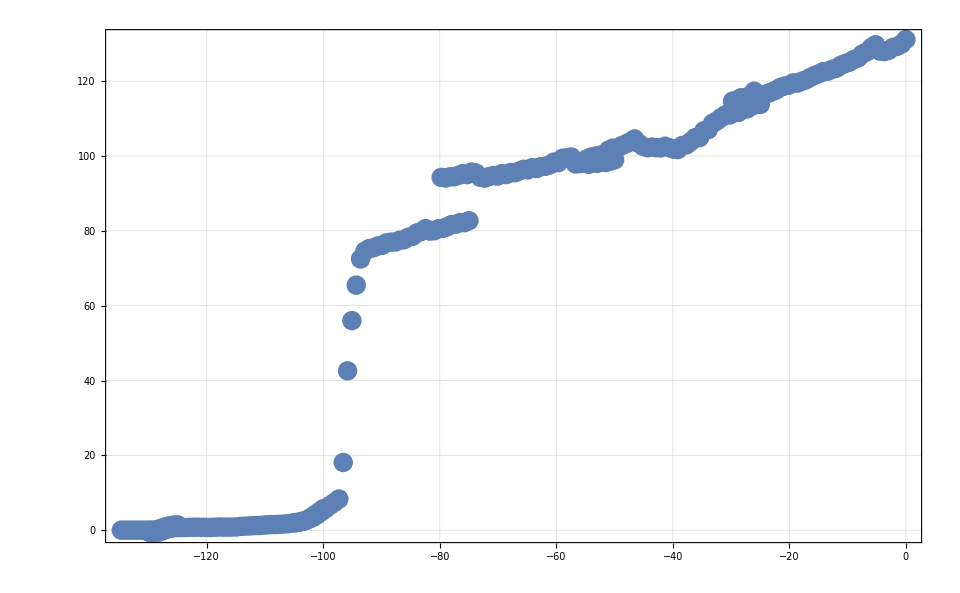

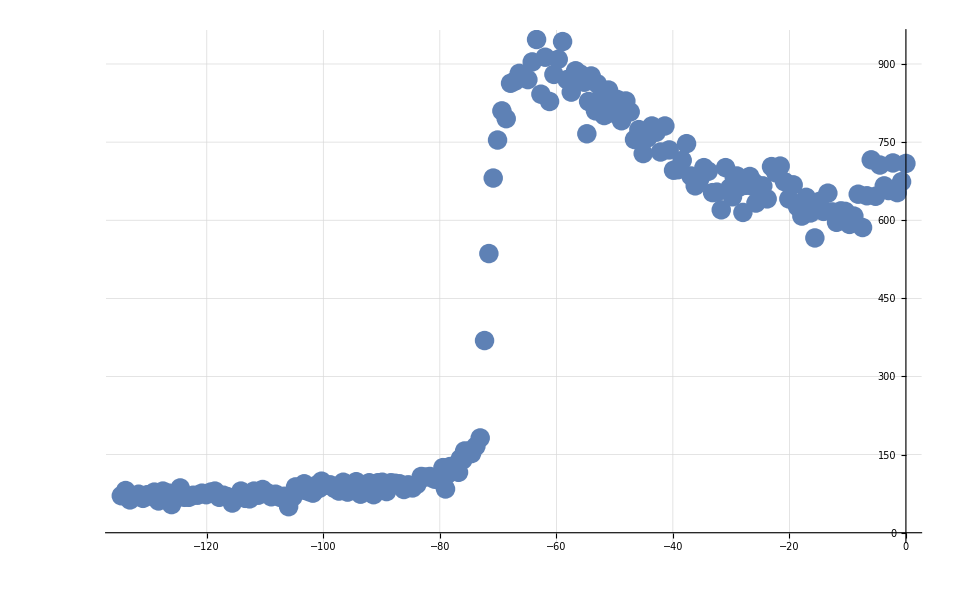

```mathematica
Clear[allDat];
cleanedFiles=Join[Take[files,{1,5}],Take[files,{7,8}]]
cleanedFiles=files;
start=22;
end=27;
For[i=start,i≤ end,i++,
header=GetFileHeaderInfo[cleanedFiles[[i]]];
magnitude=header["MagnitudeOfCurrent(*10^-X)"];
dat=GetFileDataset[files[[i]]];
newDat=dat[All,<|#,"Current(nA)"-> #Current*10^(-magnitude+9)|>&];
If[i==start,allDat=newDat,allDat=Join[allDat,newDat]]
];
ListPlot[allDat[All,{"TotalHeOffset","Current(nA)"}],PlotRange->Full,GridLines->Automatic,Frame->True,Ticks->Automatic]
ListPlot[allDat[All,{"TotalHeOffset","CountRate"}]]
```

## E_i=60eV, Sweep=2 eV

{EX2018-04-18_142916.dat,EX2018-04-18_150048.dat,EX2018-04-18_170656.dat,EX2018-04-18_170951.dat,EX2018-04-18_171257.dat,EX2018-04-18_172010.dat,EX2018-04-18_172240.dat}

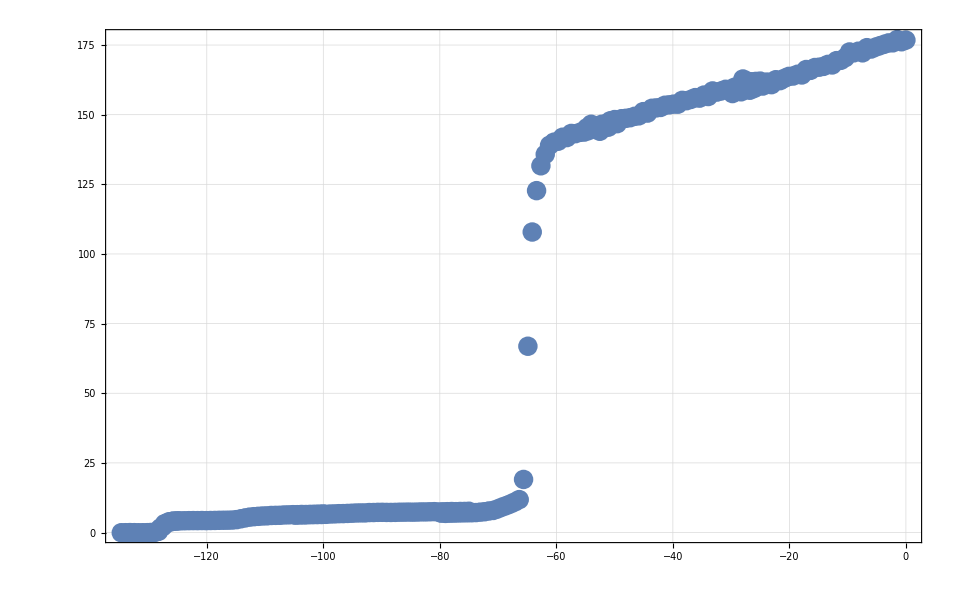

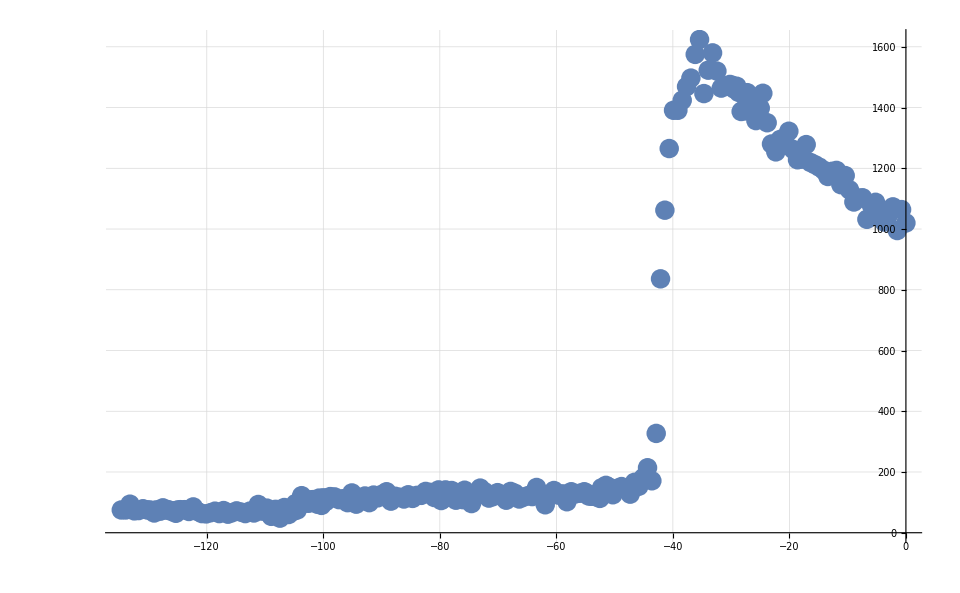

```mathematica
Clear[allDat];
cleanedFiles=Join[Take[files,{1,5}],Take[files,{7,8}]]
cleanedFiles=files;
start=28;
end=33;
For[i=start,i≤ end,i++,
header=GetFileHeaderInfo[cleanedFiles[[i]]];
magnitude=header["MagnitudeOfCurrent(*10^-X)"];
dat=GetFileDataset[files[[i]]];
newDat=dat[All,<|#,"Current(nA)"-> #Current*10^(-magnitude+9)|>&];
If[i==start,allDat=newDat,allDat=Join[allDat,newDat]]
];
ListPlot[allDat[All,{"TotalHeOffset","Current(nA)"}],PlotRange->Full,GridLines->Automatic,Frame->True,Ticks->Automatic]
ListPlot[allDat[All,{"TotalHeOffset","CountRate"}]]
```

## E_i=60eV, Sweep=23 eV

{EX2018-04-18_142916.dat,EX2018-04-18_150048.dat,EX2018-04-18_170656.dat,EX2018-04-18_170951.dat,EX2018-04-18_171257.dat,EX2018-04-18_172010.dat,EX2018-04-18_172240.dat}

39

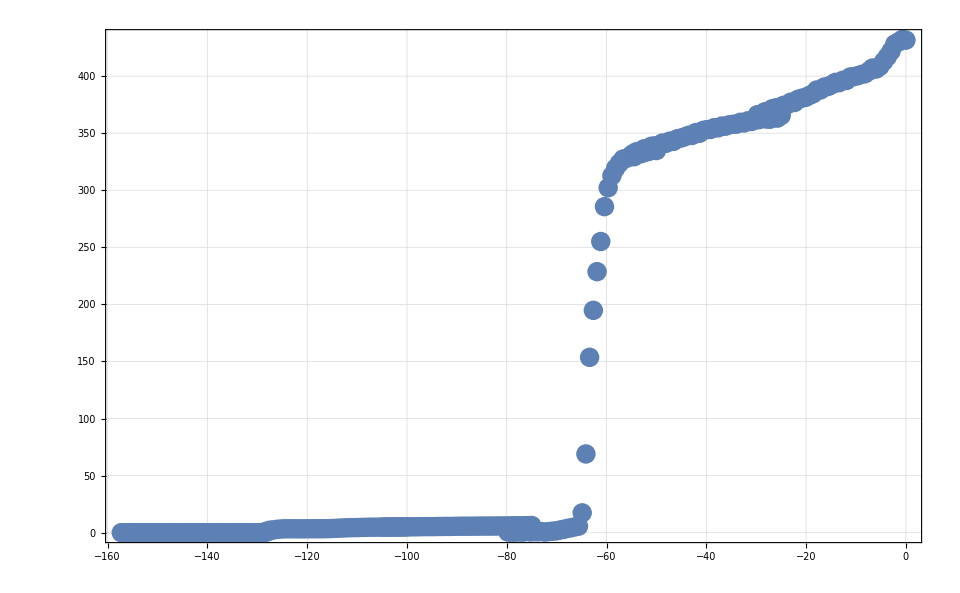

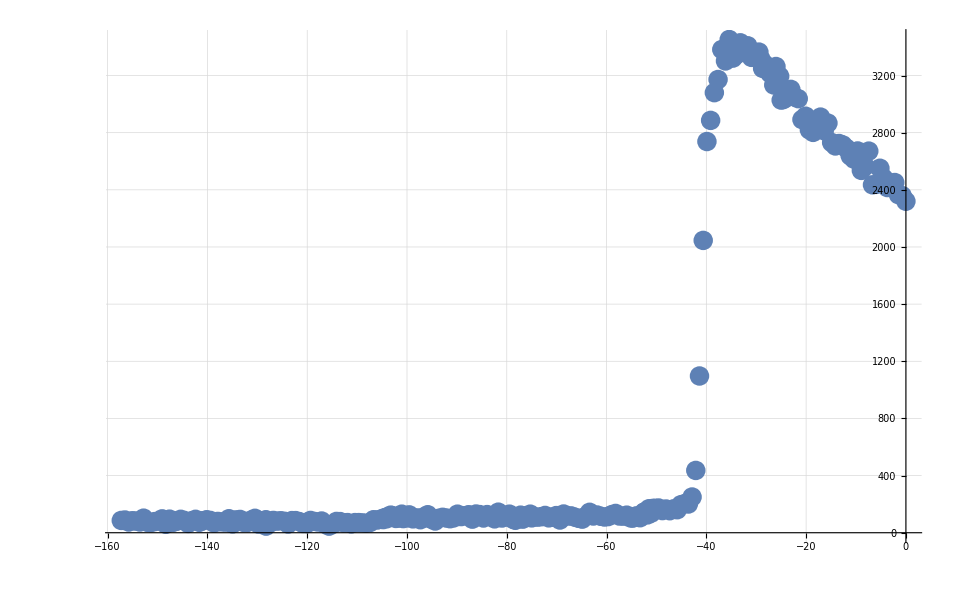

```mathematica
Clear[allDat];
cleanedFiles=Join[Take[files,{1,5}],Take[files,{7,8}]]
cleanedFiles=files;
start=34;
end=39;
For[i=start,i≤ end,i++,
header=GetFileHeaderInfo[cleanedFiles[[i]]];
magnitude=header["MagnitudeOfCurrent(*10^-X)"];
dat=GetFileDataset[files[[i]]];
newDat=dat[All,<|#,"Current(nA)"-> #Current*10^(-magnitude+9)|>&];
If[i==start,allDat=newDat,allDat=Join[allDat,newDat]]
];
ListPlot[allDat[All,{"TotalHeOffset","Current(nA)"}],PlotRange->Full,GridLines->Automatic,Frame->True,Ticks->Automatic]
ListPlot[allDat[All,{"TotalHeOffset","CountRate"}]]
```

## E_i=90eV, Sweep=2 eV

{EX2018-04-18_142916.dat,EX2018-04-18_150048.dat,EX2018-04-18_170656.dat,EX2018-04-18_170951.dat,EX2018-04-18_171257.dat,EX2018-04-18_172010.dat,EX2018-04-18_172240.dat}

44

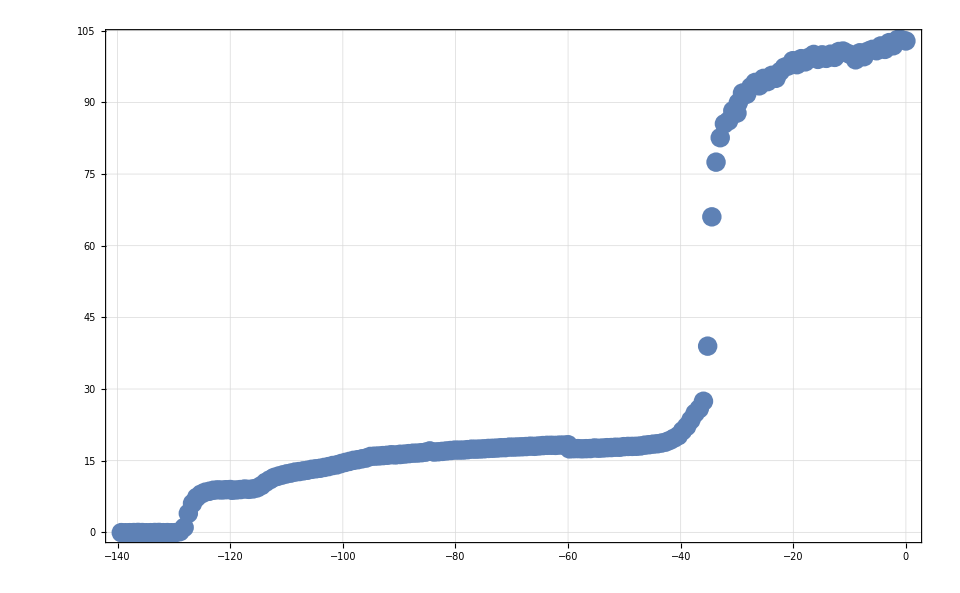

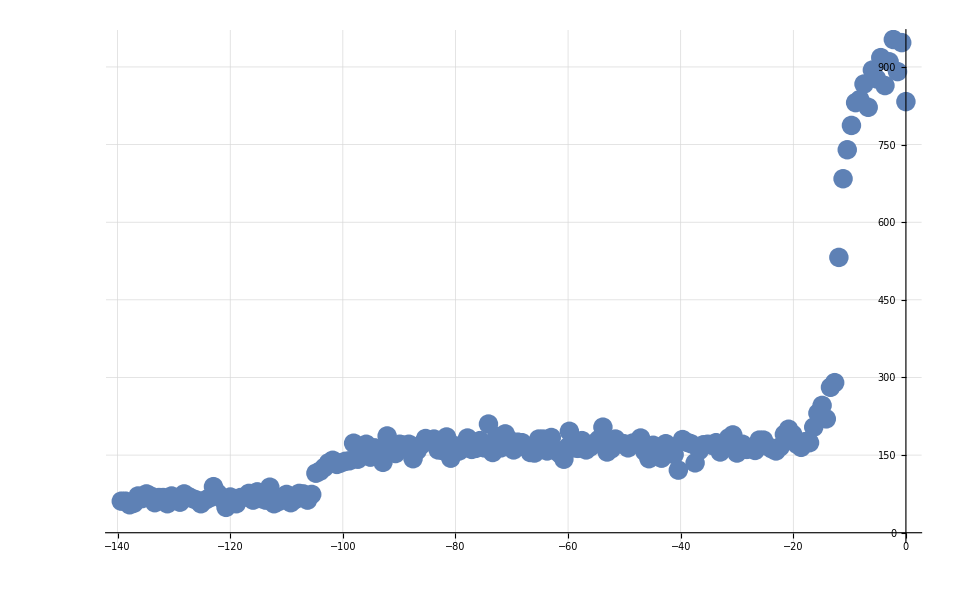

```mathematica
Clear[allDat];
cleanedFiles=Join[Take[files,{1,5}],Take[files,{7,8}]]
cleanedFiles=files;
start=40;
end=Length[files]
For[i=start,i≤ end,i++,
header=GetFileHeaderInfo[cleanedFiles[[i]]];
magnitude=header["MagnitudeOfCurrent(*10^-X)"];
dat=GetFileDataset[files[[i]]];
newDat=dat[All,<|#,"Current(nA)"-> #Current*10^(-magnitude+9)|>&];
If[i==start,allDat=newDat,allDat=Join[allDat,newDat]]
];
ListPlot[allDat[All,{"TotalHeOffset","Current(nA)"}],PlotRange->Full,GridLines->Automatic,Frame->True,Ticks->Automatic]
ListPlot[allDat[All,{"TotalHeOffset","CountRate"}],PlotRange->Full]
```

## E_i=90eV, Sweep=11 eV

{EX2018-04-18_142916.dat,EX2018-04-18_150048.dat,EX2018-04-18_170656.dat,EX2018-04-18_170951.dat,EX2018-04-18_171257.dat,EX2018-04-18_172010.dat,EX2018-04-18_172240.dat}

49

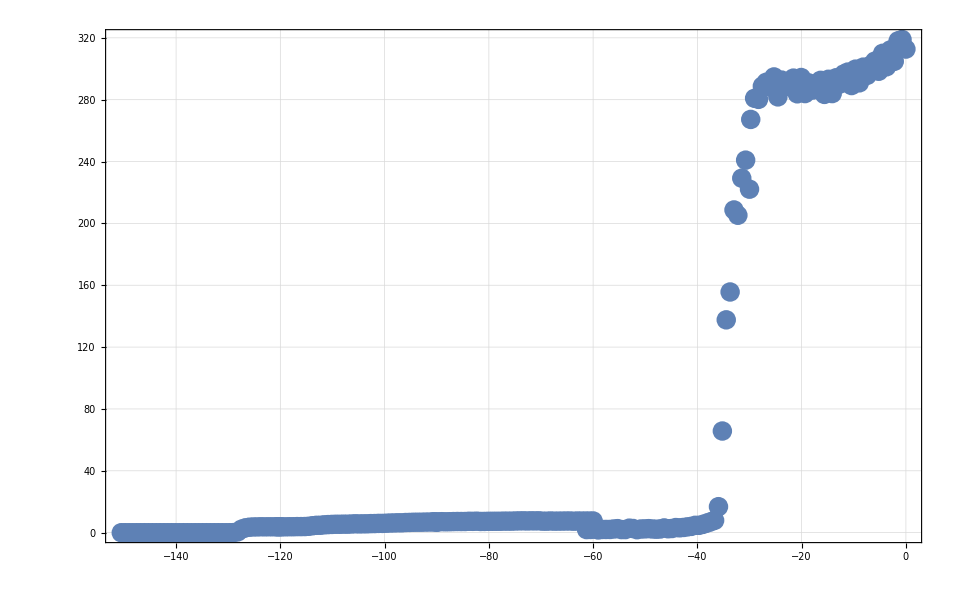

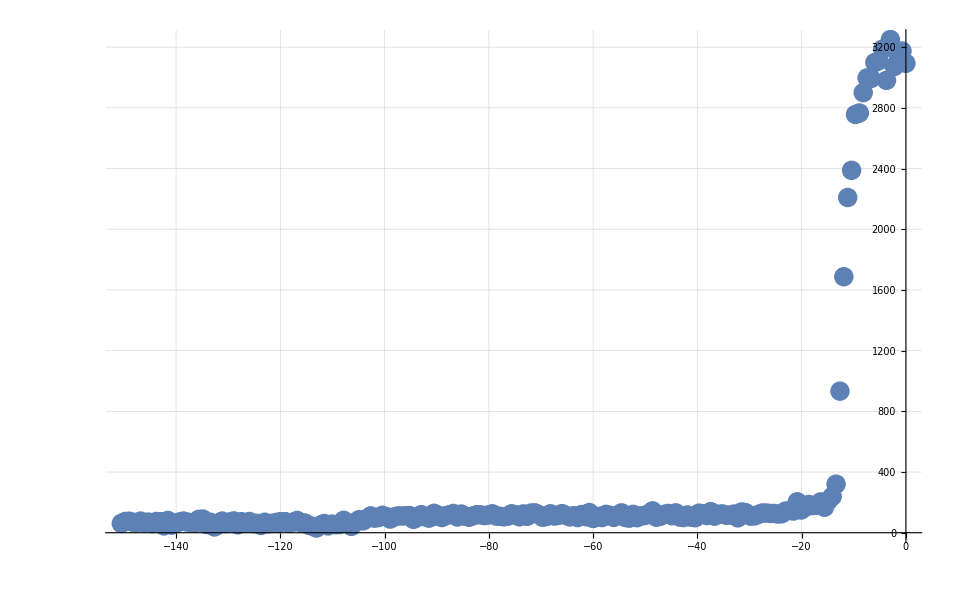

```mathematica
Clear[allDat];
cleanedFiles=Join[Take[files,{1,5}],Take[files,{7,8}]]
cleanedFiles=files;
start=45;
end=Length[files]-2
For[i=start,i≤ end,i++,
header=GetFileHeaderInfo[cleanedFiles[[i]]];
magnitude=header["MagnitudeOfCurrent(*10^-X)"];
dat=GetFileDataset[files[[i]]];
newDat=dat[All,<|#,"Current(nA)"-> #Current*10^(-magnitude+9)|>&];
If[i==start,allDat=newDat,allDat=Join[allDat,newDat]]
];
ListPlot[allDat[All,{"TotalHeOffset","Current(nA)"}],PlotRange->Full,GridLines->Automatic,Frame->True,Ticks->Automatic]
ListPlot[allDat[All,{"TotalHeOffset","CountRate"}],PlotRange->Full]
```

## E_i=90eV, Sweep=21 eV, BGP=200 mTorr

{EX2018-04-18_142916.dat,EX2018-04-18_150048.dat,EX2018-04-18_170656.dat,EX2018-04-18_170951.dat,EX2018-04-18_171257.dat,EX2018-04-18_172010.dat,EX2018-04-18_172240.dat}

50

54

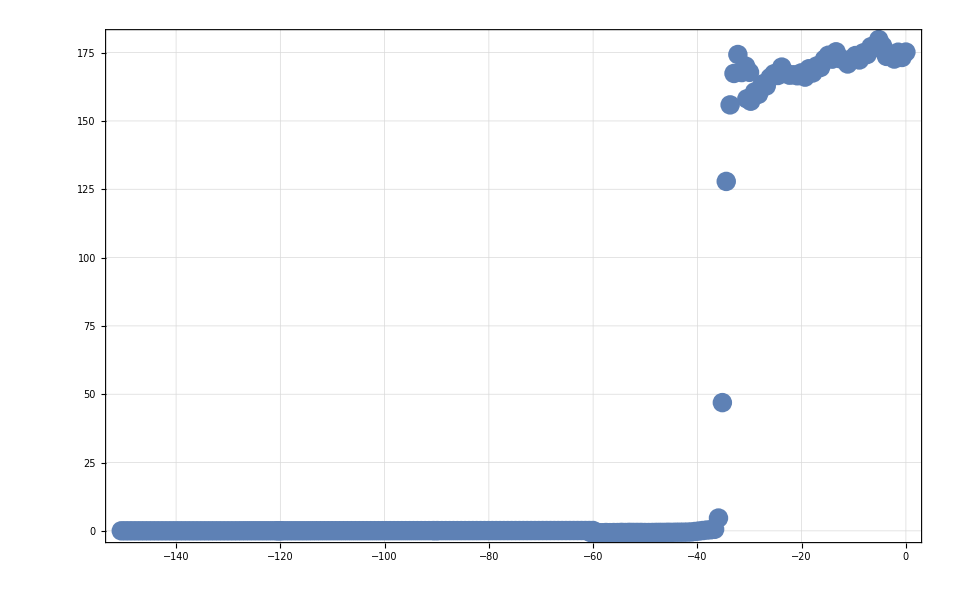

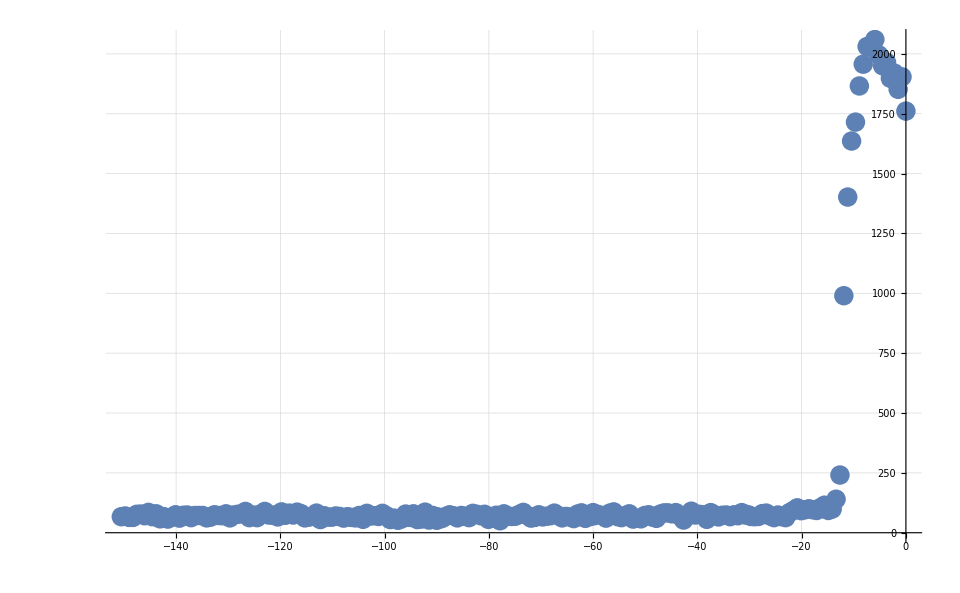

```mathematica
Clear[allDat];
cleanedFiles=Join[Take[files,{1,5}],Take[files,{7,8}]]
cleanedFiles=files;
start=50
end=Length[files]
For[i=start,i≤ end,i++,
header=GetFileHeaderInfo[cleanedFiles[[i]]];
magnitude=header["MagnitudeOfCurrent(*10^-X)"];
dat=GetFileDataset[files[[i]]];
newDat=dat[All,<|#,"Current(nA)"-> #Current*10^(-magnitude+9)|>&];
If[i==start,allDat=newDat,allDat=Join[allDat,newDat]]
];
ListPlot[allDat[All,{"TotalHeOffset","Current(nA)"}],PlotRange->Full,GridLines->Automatic,Frame->True,Ticks->Automatic]
ListPlot[allDat[All,{"TotalHeOffset","CountRate"}],PlotRange->Full]
```